# 3.3

ReplaceAll::reps: {#1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

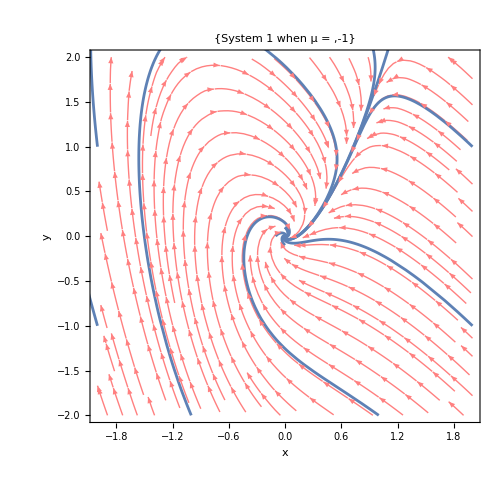

```mathematica
ClearAll["Global`*"]

(*Define systems*)
mu=-1;
eq1=x'[t]==mu*x[t]+y[t]-x[t]^2;
eq2=y'[t]== -x[t]+mu*y[t]+2*x[t]^2;
system={eq1,eq2};

startPt={{x[0]==-2,y[0]==-1},{x[0]==-2,y[0]==1},{x[0]==2,y[0]==-1},{x[0]==2,y[0]==1},{x[0]==-1,y[0]==-2},{x[0]==1,y[0]==-2},{x[0]==0,y[0]==-0.1},{x[0]==0,y[0]==0.1},{x[0]==-0.1,y[0]== 0},{x[0]==0,y[0]==0.1}};

t0=0;
tMax=10;
sol=Table[NDSolve[{system,mu},{x,y},{t,t0,tMax}],{mu,startPt}];
sp=StreamPlot[{mu*x+y-x^2,-x+mu*y+2*x^2},{x,-2,2},{y,-2,2},StreamColorFunction->None,StreamStyle->Pink,PlotRange->All,ImageSize->500];
tp=ParametricPlot[Evaluate[{x[t],y[t]}/. #]&/@sol,{t,t0,tMax}];
Show[sp,tp,FrameLabel->{"x","y"},PlotLabel->{"System 1 when μ = ",mu}]
```

10

ReplaceAll::reps: {#1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

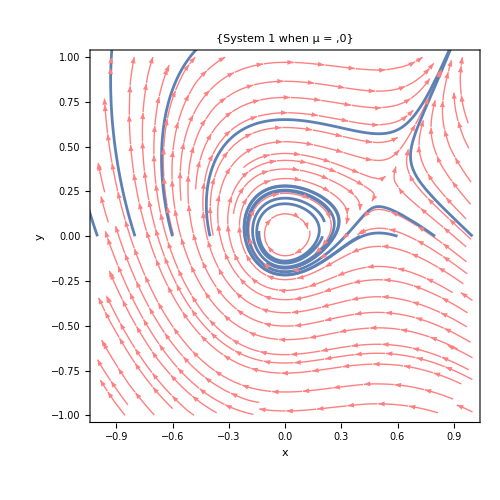

```mathematica
ClearAll["Global`*"]

mu=0;
eq1=x'[t]==mu*x[t]+y[t]-x[t]^2;
eq2=y'[t]== -x[t]+mu*y[t]+2*x[t]^2;
system={eq1,eq2};
nTraj=10
startPt=Table[{x[0]==-1+2*i/nTraj,y[0]==0},{i,0,nTraj}];
(*startPt={{x[0]==-2,y[0]==-1},{x[0]==-2,y[0]==1},{x[0]==2,y[0]==-1},{x[0]==2,y[0]==1},{x[0]==-1,y[0]==-2},{x[0]==1,y[0]==-2},{x[0]==0,y[0]==-0.1},{x[0]==0,y[0]==0.1},{x[0]==-0.1,y[0]== 0},{x[0]==0,y[0]==0.1}};*)

t0=0;
tMax=10;
sol=Table[NDSolve[{system,mu},{x,y},{t,t0,tMax}],{mu,startPt}];
sp=StreamPlot[{mu*x+y-x^2,-x+mu*y+2*x^2},{x,-1,1},{y,-1,1},StreamColorFunction->None,StreamStyle->Pink,PlotRange->All,ImageSize->500];
tp=ParametricPlot[Evaluate[{x[t],y[t]}/. #]&/@sol,{t,t0,tMax}];
Show[sp,tp,FrameLabel->{"x","y"},PlotLabel->{"System 1 when μ = ",mu}]
```

ReplaceAll::reps: {#1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

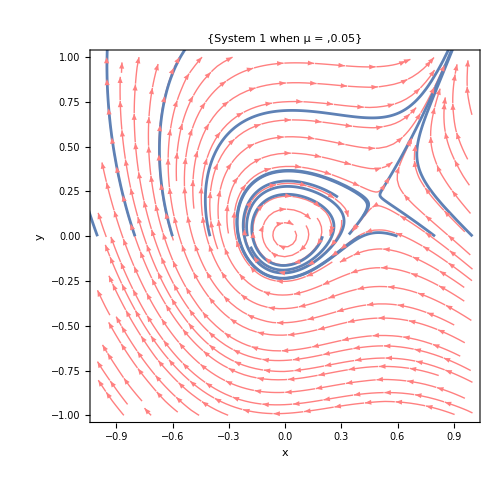

```mathematica
mu=0.05;
eq1=x'[t]==mu*x[t]+y[t]-x[t]^2;
eq2=y'[t]== -x[t]+mu*y[t]+2*x[t]^2;
system={eq1,eq2};

startPt=Table[{x[0]==-1+2*i/nTraj,y[0]==0},{i,0,nTraj}];(*startPt={{x[0]==-2,y[0]==-1},{x[0]==-2,y[0]==1},{x[0]==2,y[0]==-1},{x[0]==2,y[0]==1},{x[0]==-1,y[0]==-2},{x[0]==1,y[0]==-2},{x[0]==0,y[0]==-0.1},{x[0]==0,y[0]==0.1},{x[0]==-0.1,y[0]== 0},{x[0]==0,y[0]==0.1}};*)

t0=0;
tMax=10;
sol=Table[NDSolve[{system,mu},{x,y},{t,t0,tMax}],{mu,startPt}];
sp=StreamPlot[{mu*x+y-x^2,-x+mu*y+2*x^2},{x,-1,1},{y,-1,1},StreamColorFunction->None,StreamStyle->Pink,PlotRange->All,ImageSize->500];
tp=ParametricPlot[Evaluate[{x[t],y[t]}/. #]&/@sol,{t,t0,tMax}];
Show[sp,tp,FrameLabel->{"x","y"},PlotLabel->{"System 1 when μ = ",mu}]
```

ReplaceAll::reps: {#1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

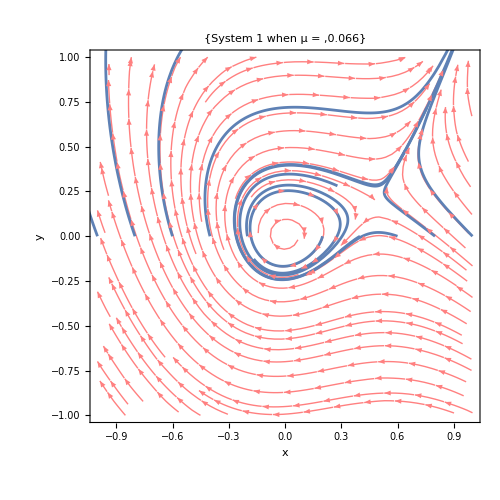

```mathematica
mu=0.066;
eq1=x'[t]==mu*x[t]+y[t]-x[t]^2;
eq2=y'[t]== -x[t]+mu*y[t]+2*x[t]^2;
system={eq1,eq2};

startPt=Table[{x[0]==-1+2*i/nTraj,y[0]==0},{i,0,nTraj}];
(*startPt={{x[0]==-2,y[0]==-1},{x[0]==-2,y[0]==1},{x[0]==2,y[0]==-1},{x[0]==2,y[0]==1},{x[0]==-1,y[0]==-2},{x[0]==1,y[0]==-2},{x[0]==0,y[0]==-0.1},{x[0]==0,y[0]==0.1},{x[0]==-0.1,y[0]== 0},{x[0]==0,y[0]==0.1},{x[0]==0.2,y[0]==0}};*)

t0=0;
tMax=10;
sol=Table[NDSolve[{system,mu},{x,y},{t,t0,tMax}],{mu,startPt}];
sp=StreamPlot[{mu*x+y-x^2,-x+mu*y+2*x^2},{x,-1,1},{y,-1,1},StreamColorFunction->None,StreamStyle->Pink,PlotRange->All,ImageSize->500];
tp=ParametricPlot[Evaluate[{x[t],y[t]}/. #]&/@sol,{t,t0,tMax}];
Show[sp,tp,FrameLabel->{"x","y"},PlotLabel->{"System 1 when μ = ",mu}]
```

ReplaceAll::reps: {#1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

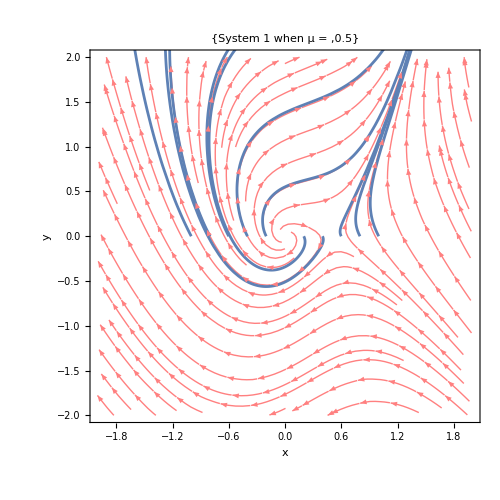

```mathematica
mu=0.5;
eq1=x'[t]==mu*x[t]+y[t]-x[t]^2;
eq2=y'[t]== -x[t]+mu*y[t]+2*x[t]^2;
system={eq1,eq2};
startPt=Table[{x[0]==-1+2*i/nTraj,y[0]==0},{i,0,nTraj}];
(*startPt={{x[0]==-2,y[0]==-1},{x[0]==-2,y[0]==1},{x[0]==2,y[0]==-1},{x[0]==2,y[0]==1},{x[0]==-1,y[0]==-2},{x[0]==1,y[0]==-2},{x[0]==0,y[0]==-0.1},{x[0]==0,y[0]==0.1},{x[0]==-0.1,y[0]== 0},{x[0]==0,y[0]==0.1}};*)

t0=0;
tMax=10;
sol=Table[NDSolve[{system,mu},{x,y},{t,t0,tMax}],{mu,startPt}];
sp=StreamPlot[{mu*x+y-x^2,-x+mu*y+2*x^2},{x,-2,2},{y,-2,2},StreamColorFunction->None,StreamStyle->Pink,PlotRange->All,ImageSize->500];
tp=ParametricPlot[Evaluate[{x[t],y[t]}/. #]&/@sol,{t,t0,tMax}];
Show[sp,tp,FrameLabel->{"x","y"},PlotLabel->{"System 1 when μ = ",mu}]
```

c)